-Graphics-

## Lesson 7: Exact equations

-Graphics-

## Overview

In order to solve linear and separable equations, it is best to transform the equation into an easily integrable form.

This lesson will examine exact equations, which are neither separable nor linear, yet can be transformed into a more manageable form that can be directly solved.

This will be done by examining the partial derivatives of an auxiliary function.

It is important to remember that for an arbitrary first-order ODE, there is no general method for solving the equation.

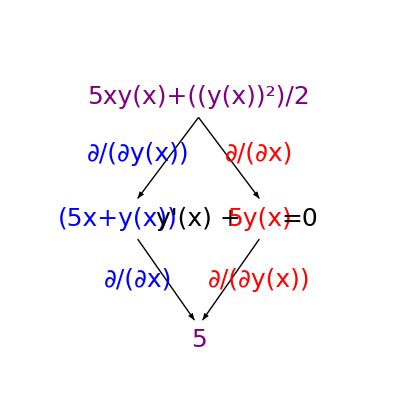

```mathematica
Show[Graphics[Arrow[{{0,1},{.75,0}}]],Graphics[Arrow[{{0,1},{-.75,0}}]],Graphics[Arrow[{{.75,-.5},{.05,-1.5}}]],Graphics[Arrow[{{-.75,-.5},{-0.05,-1.5}}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[(5x+y(x))],25,Blue],{-1,-.25}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[y'(x) +],25],{0,-.25}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[5y(x)],25,Red],{.75,-.25}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[=0],25],{1.25,-.25}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[5xy(x)+(y(x))^2/2],25,Purple],{0,1.25}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[∂/(∂x)],25,Red],{.75,.55}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[∂/(∂y(x))],25,Blue],{-.75,.55}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[∂/(∂x)],25,Blue],{-.75,-1}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[∂/(∂y(x))],25,Red],{.75,-1}]],Graphics[Inset[Style[HoldForm@@MakeExpression@MakeBoxes@TraditionalForm[5],25,Purple],{0,-1.75}]],PlotRange->{{-2,2},{-2,2}}]
```

## Exact Equations

Begin with a general first-order differential equation of the form:

N(t,y(t))(ⅆy(t))/ⅆt+M(t,y(t))=0

Suppose there is an auxiliary function ϕ(t,y(t)) such that:

(∂ϕ)/(∂t)=M(t,y(t))

(∂ϕ)/(∂y(t))=N(t,y(t))

Then, rewrite the differential equation as:

(∂ϕ)/(∂y(t))(ⅆy(t))/ⅆt+(∂ϕ)/(∂t)=0

Recall that from the chain rule (∂ϕ)/(∂y(t))(ⅆy(t))/ⅆt=(∂ϕ)/(∂t).

Thus, the equation can simply be written as:

(∂ϕ)/(∂t)=0

Therefore, there is an implicit form of the solution:

ϕ(t,y(t))=C

## Classify Equation as Exact

Verify that the equation is exact, then find its solution:

5 e^(y(t))+5 t e^(y(t))(ⅆy(t))/ⅆt=0

The important step is to recognize the (∂ϕ)/(∂t) and (∂ϕ)/(∂y(t)) terms in the equation:

(∂ϕ)/(∂t)=5 e^(y(t))

(∂ϕ)/(∂y(t))=5 t e^(y(t))

Use DSolveValue to find ϕ(t,y(t)):

```mathematica
DSolveValue[{D[ϕ[t,y],t]==5Exp[y],D[ϕ[t,y],y]==5 t Exp[y]},ϕ[t,y],{t,y}]
```

5 ⅇ^y t+C[1]

Since an implicit form of the solution is ϕ(t,y(t))=C, you can combine the two arbitrary constants and write this as:

5 t e^(y(t))=C_1

## Classify Equation as Exact

Use Solve to obtain an explicit expression for the solution:

```mathematica
Solve[5 t Exp[y[t]]==Subscript[C, 1],y[t],Reals]
```

{{y[t]→ConditionalExpression[Log[C_1/(5 t)], (t>0&&C_1>0)||(t<0&&C_1<0)]}}

The answer can be verified by using DSolveValue:

```mathematica
DSolveValue[5Exp[y[t]]+5t Exp[y[t]]y'[t]==0,y[t],t]
```

C[1]-Log[t]

These two solutions are equivalent after applying the properties of Log:

Log[C_1/(5 t)]=Log[C_1/5]-Log[t]=C_2-Log[t]

where Log[C_1/5]=C_2 was defined as the arbitrary constant.

## Determine Systematically

There is a relatively quick way to recognize an exact equation when the auxiliary function ϕ(x,t) is not obvious.

Begin with a general first-order differential equation of the form:

N(t,y(t))(ⅆy(t))/ⅆt+M(t,y(t))=0

If there is an auxiliary function ϕ(t,y(t)) such that:

(∂ϕ)/(∂t)=M(t,y(t)),  (∂ϕ)/(∂y(t))=N(t,y(t))

then it must also be true that:

∂/(∂t)N(t,y(t))=∂/(∂t)(∂ϕ)/(∂y(t))
	=∂/(∂y(t))(∂ϕ)/(∂t)
	=∂/(∂y(t))M(t,y(t))

So it can be determined that an equation is exact if and only if:

∂/(∂t)N(t,y(t))=∂/(∂y(t))M(t,y(t))

## Determine Systematically

Determine if the following equation is exact:

2f(x)x+(f(x))^2+(x^2+x f(x))(ⅆf(x))/ⅆx

To do this, check if it is true that:

∂/(∂x)N(x,f(x)) =∂/(∂f(x))M(x,f(x))

This can be easily done through the use of the function D:

```mathematica
m=2f x+f^2;
n=x^2+x f;
D[m,f]==D[n,x]//Simplify
```

f==0

After applying the function Simplify, the relation is shown to not be true for all functions f(x).

Thus, the equation is not exact.

## Example 1

Determine if the equation is exact. If it is, find the solution:

(g(x))/x+6x+g'(x)(ln(x)-2)=0

Check if it is true that:

∂/(∂x)N(x,g(x)) =∂/(∂g(x))M(x,g(x))

This can be easily done through the use of the function D:

```mathematica
m=g[x]/x+6x;
n=Log[x]-2;
D[m,g[x]]==D[n,x]//Simplify
```

True

After applying the function Simplify, the relation is shown to be True, so the equation is exact.

## Example 1

Because you know:

(∂ϕ)/(∂x)=M(x,g(x))

(∂ϕ)/(∂g(x))=N(x,g(x))

you can find ϕ(x,g(x)) by integrating the known functions M(x,g(x)) or N(x,g(x)) giving:

ϕ(x,g(x)) = g(x)ln(x)+3 x^2-2g(x)

An expression involving the solution g(x) can then be written using ϕ(x,g(x))=C_1:

```mathematica
sln=g[x]Log[x]+3x^2-2g[x]==Subscript[C, 1]
```

3 x^2-2 g[x]+g[x] Log[x]==C_1

Use Solve to obtain an explicit expression for the solution:

```mathematica
Solve[sln,g[x],Reals]
```

{{g[x]→ConditionalExpression[(-3 x^2+C_1)/(-2+Log[x]), 0<x<ⅇ^2||x>ⅇ^2]}}

The answer can be verified by using DSolveValue:

```mathematica
DSolveValue[m+n*g'[x]==0,g[x],x]//FullSimplify
```

(-3 x^2+C[1])/(-2+Log[x])

## Example 2

Determine if the equation is exact. If it is, find the solution:

3y(x)e^(3y(x)x)+x+y'(x)(3x e^(3y(x)x))=0

Check if it is true that:

∂/(∂x)N(x,y(x)) =∂/(∂y(x))M(x,y(x))

This can be easily done through the use of the function D:

```mathematica
m=3 y Exp[3 y x]+x;
n=3 x Exp[3y x];
D[m,y]==D[n,x]//Simplify
```

True

Thus the equation is exact and the auxiliary function ϕ(x,y(x)) can be found.

## Example 2

Using:

(∂ϕ)/(∂x)=M(x,g(x))

(∂ϕ)/(∂g(x))=N(x,g(x))

find through integration that:

ϕ(x,y(x)) = e^(3y(x) x)+x^2/2

Write an expression involving the solution, y(x), using ϕ(x,y(x))=C_1:

```mathematica
sln=Exp[3y[x]x]+x^2/2==Subscript[C, 1]
```

ⅇ^(3 x y[x])+x^2/2==C_1

Use Solve to obtain an explicit expression for the solution:

```mathematica
Solve[sln,y[x],Reals]
```

{{y[x]→ConditionalExpression[Log[1/2 (-x^2+2 C_1)]/(3 x), C_1>x^2/2]}}

The answer can be verified by using DSolveValue:

```mathematica
DSolveValue[3 y[x] Exp[3 y[x] x]+x+3 x Exp[3y[x] x]y'[x]==0,y[x],x]//Quiet
```

Log[-(-1)^(1/3) (-x^2/2+C[1])^(1/3)]/x

These two solutions are equivalent aside from a phase factor due to the arbitrary coefficient C_1.

## Summary

This lesson discussed a subclass of first-order differential equations called exact equations.

These differential equations take the form:

N(t,y(t))(ⅆy(t))/ⅆt+M(t,y(t))=0

First-order ODEs are classified as exact when:

∂/(∂x)N(x,g(x))=∂/(∂g(x))M(x,g(x))

When the equation is exact, an implicit form of the solution becomes:

ϕ(t,y(t))=C